```mathematica
(*rotation matrix*)
rot[th_] :=({{1, 0, 0, 0}, {0, Cos[2 th], Sin[2th], 0}, {0, -Sin[2 th], Cos[2th], 0}, {0, 0, 0, 1}})
(*waveplate matrix*)
wp[th_] :=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[th], Sin[th]}, {0, 0, -Sin[th], Cos[th]}})
(*polariser matrix*)
pol := 1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
matrix =pol.pol
```

```mathematica
{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

matrix = pol.rot.pol
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}.rot.{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
matrix =(pol.rot[3π/4-theta-a].pol.rot[theta+a].{I0,0,0,0} )[[1]]
Plot[matrix/.{I0->1,a->49.6π/180},{theta,0,2π}]
```

I0 (1/4+1/4 Cos[2 (-a+(3 π)/4-theta)])

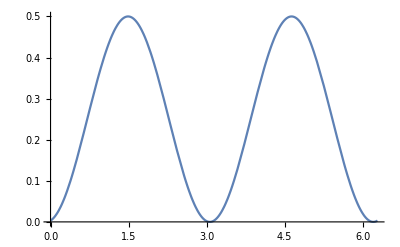

-Graphics-